```mathematica
SetDirectory[NotebookDirectory[]]
<<MaTeX`
```

/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö

```mathematica
files=FileNames["*.csv","Pythia/STAR9"];
data=Import/@files;
```

```mathematica
labels={
"1.0<p_T^1<1.4, 1.4<p_T^2<2.0",
"1.0<p_T^1<1.4, 2.0<p_T^2<2.4",
"1.0<p_T^1<1.4, 2.4<p_T^2<2.8",
"1.0<p_T^1<1.4, 2.8<p_T^2<5.0",
"1.4<p_T^1<2.0, 2.0<p_T^2<2.4",
"1.4<p_T^1<2.0, 2.4<p_T^2<2.8",
"1.4<p_T^1<2.0, 2.8<p_T^2<5.0",
"2.0<p_T^1<2.4, 2.4<p_T^2<2.8",
"2.0<p_T^1<2.4, 2.8<p_T^2<5.0",
"2.4<p_T^1<2.8, 2.8<p_T^2<5.0"
};
ranges={
40,40,40,40,
15,25,15,
5,2,
0.8
};
```

```mathematica
NormalizationConstant[data_]:=Total[data[[All,2]]]*π
NormalizeBy[data_,const_]:=data.DiagonalMatrix[{1,const}]
xPoints=Table[x0,{x0,π/40-π/2,3π/2,π/20}];
ReflectedData[data_]:=ArrayPad[data[[All,2]],(Length[xPoints]-Length[data[[All,2]]])/2,"Reversed"]
Reconstruct[data_]:=Transpose[{xPoints,ReflectedData[data]}]
```

```mathematica
NormalizeData[data_,scale_,method_]:=NormalizeBy[data,scale/NormalizationConstant[data]]/;method=="Count"
NormalizeData[data_,scale_,method_]:=data/;method=="None"
NormalizeData[data_,scale_,method_]:=NormalizeBy[data,scale/method]/;NumberQ[method]
```

```mathematica
Ranges[method_]:=ranges/;method=="STAR"
Ranges[method_]:=ConstantArray[All,Length@ranges]/;method=="None"
```

```mathematica
AxesLabels[method_]:={"\\Delta\\phi","N\\times 10^{-3}"}/;method=="STAR"
AxesLabels[method_]:={"\\Delta\\phi","N"}/;method=="None"
```

```mathematica
GeneratePlots[normalization_,decorations_]:=ListPlot[NormalizeData[Reconstruct[#[[1]]],10^3,normalization],
AxesLabel->MaTeX/@AxesLabels[decorations],
PlotLabel->MaTeX@#[[2]],
PlotRange->{All,{0,#[[3]]}},
AxesOrigin->{-π/2,0},
Ticks->{{0,π/2,π},Automatic}
]&/@Transpose[{data,labels,Ranges[decorations]}]
```

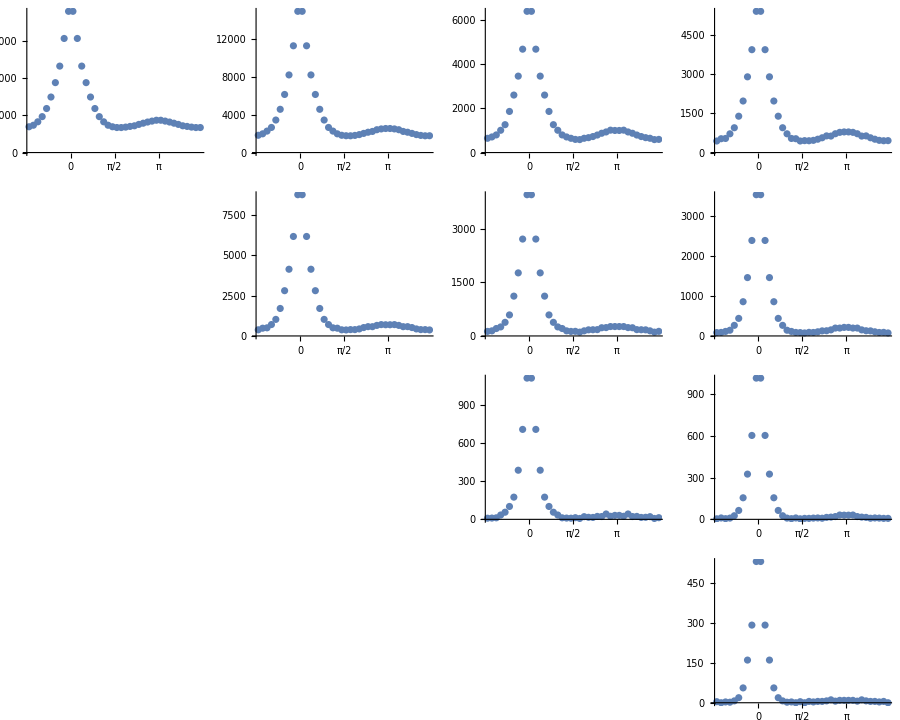

```mathematica
plots=GeneratePlots["None","None"];
grid=GraphicsGrid[{
{plots[[1]],plots[[2]],plots[[3]],plots[[4]]},
{Null,plots[[5]],plots[[6]],plots[[7]]},
{Null,Null,plots[[8]],plots[[9]]},
{Null,Null,Null,plots[[10]]}
},ItemAspectRatio->0.8,ImageSize->900]
```

```mathematica
model=NonlinearModelFit[Reconstruct[data[[1]]],a1 Exp[-x^2/(2 c1^2)]+a2 Exp[-(x-π)^2/(2 c2^2)]+p,{{a1,60000},{c1,0.5},{a2,2500},{c2,0.5},{p,10000}},x,MaxIterations->1000000,ConfidenceLevel->0.9999]
```

FittedModel[14628.5+58045.6 ⅇ^(-«19» x^2)+2902.11 ⅇ^(-3.81475 (-π+x)^2)]

```mathematica
model["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a1 | 58045.6 | 1210.63 | 47.9466 | 1.62087×10^-33
c1 | 0.408073 | 0.0107511 | 37.9563 | 4.96088×10^-30
a2 | 2902.11 | 1277.91 | 2.27098 | 0.0294081
c2 | 0.362036 | 0.199763 | 1.81233 | 0.0785219
p | 14628.5 | 538.923 | 27.144 | 4.22889×10^-25

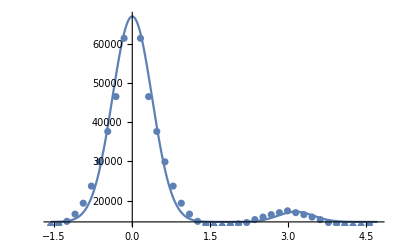

```mathematica
Show[Plot[model[x],{x,-π/2,3π/2}],plots[[1]]]
```

```mathematica
Manipulate[Show[plots[[1]],Plot[a1 Exp[-x^2/(2 c1^2)]+a2 Exp[-(x-π)^2/(2 c2^2)]+p,{x,-π/2,3π/2}]],{a1,50000,60000},{c1,0.1,1},{a2,0,10000},{c2,0.1,1},{p,-30000,30000}]
```

General::munfl: Exp[-1110.27] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
Export["STAR.pdf",grid];
```